## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["../_Data/supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeFunc[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
incidFunc[[All,selectPos]]
];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
segments={1243,1248,1250,1252,1254,1257};
nets=Table[
makeNet[segments[[c]],segments[[c+1]]-1]
,{c,1,Length@segments-1}];
```

```mathematica
(*(* This one takes some time *)
nets=ParallelTable[makeNet[year,year],{year,yearList}];*)
```

### Graphics

```mathematica
Needs["PlotLegends`"];
colors={Directive[(*Green*)RGBColor[0.34398, 0.49112, 0.89936],Thick],Directive[(*Blue*)RGBColor[0.97, 0.606, 0.081],(*Dashing[0.015],*)Thick](*Directive[Black,Thick]*),Directive[(*Black*)RGBColor[0.09096, 0.6296, 0.85532],Thick,DotDashed],Directive[(*Blue*)RGBColor[0.448, 0.69232, 0.1538],Dashing[0.03],Thick],Directive[(*Red*)RGBColor[0.62168, 0.2798, 0.6914],Thick,Dashing[0.015]],Directive[(*Red*)RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thickness[0.02]]};
markSize=10;
marker2=Graphics[{Green,Disk[{1/2,1/2}]},ImageSize->markSize];
marker3=Graphics[{EdgeForm[Directive[Thick,RGBColor[0,0,0]]],White,Disk[{1/2,1/2}]},ImageSize->markSize];
marker4=Graphics[{Blue,Disk[{1/2,1/2}]},ImageSize->markSize];
marker5=Graphics[{EdgeForm[Directive[Thick,Red]],White,Disk[{1/2,1/2}]},ImageSize->markSize];
marker1=Graphics[{Black,Polygon[-1/2+2{{0,0},{0,1},{1,1},{1,0}}]},ImageSize->markSize];
marker6=Graphics[{Black,Thick,Line[{{.5,-1},{.5,2}}]},ImageSize->0.5markSize];
markers={marker1,marker2,marker3,marker4,marker5,marker6};
```

```mathematica
marker1=Graphics[{EdgeForm[Directive[Thick,RGBColor[0,0,0],Opacity[1]]],White,Disk[]},ImageSize->14];
marker2=Graphics[{EdgeForm[Directive[Thick,RGBColor[1,0,0],Opacity[1]]],RGBColor[1,1,1],Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->15];
marker3=Graphics[{RGBColor[0,0,1],Polygon[{{1/2,0},{0,1/2},{1/2,1},{1,1/2}}]},ImageSize->15];
```

```mathematica
(* Overlays for the timeline figures *)
shade=ListPlot[Transpose@{{1248+7/12,1249+8/12},ConstantArray[ee,2]},Joined->True,Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]]];
line=ListPlot[{{1230,ee},{1253,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
line1=ListPlot[{{1230+0.5,ee},{1253+0.5,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
```

## Global network measures

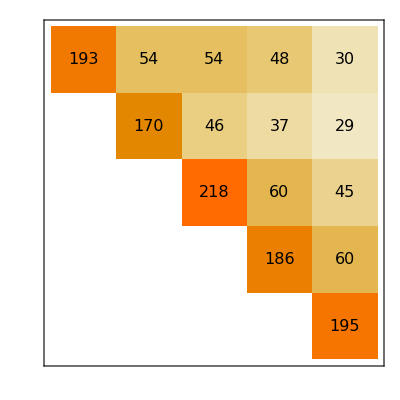

```mathematica
MatrixPlot[
Table[
If[i≤j,
Length@Intersection[
ConnectedComponents[nets[[i]][[2]]][[1]],ConnectedComponents[nets[[j]][[2]]][[1]]
],-1]
,{i,1,Length@nets},{j,1,Length@nets}]
,ColorFunction->Automatic,PlotRange->{0,320},ClippingStyle->White,FrameStyle->Directive[White],FrameTicks->{{None,Table[
{c,ToString@cezury[[c]]<>"-\n-"<>ToString[segments[[c+1]]-1]}
,{c,1,Length@segments-1}]},{None,Table[
{c,ToString@segments[[c]]<>"-\n-"<>ToString[segments[[c+1]]-1]}
,{c,1,Length@segments-1}]}},FrameTicksStyle->Directive[FontFamily->"Helvetica",Black,14],
Epilog->Flatten@Table[
Inset[Style[
ToString@Length@Intersection[
ConnectedComponents[nets[[i]][[2]]][[1]],ConnectedComponents[nets[[j]][[2]]][[1]]
],FontFamily->"Helvetica",Black,16
],{i,6-j}-0.5]
,{i,1,Length@nets},{j,1,i}]
]
```

```mathematica
chosen=Union[Flatten[
Table[
ConnectedComponents[nets[[i]][[2]]][[1]]
,{i,1,Length@nets}]
,1]/.{x_,_}:>x];
chosen//Length
```

684

### Korelacja funkcji z centralnością

#### Prepare a dataset with ranks and centralities

```mathematica
ranks=Join[Thread[funcList[[All,2]]->(funcList[[All,3]])],{0->"NA",1.->"witness"}];
funcDS=(*Dataset@*)Table[
(*Switch[c,1,Import["funcDS_1.m"],2,Import["funcDS_2.m"],4,Import["funcDS_4.m"],
_,*)
temp=makeFunc[segments[[c]],segments[[c+1]]-1]/.ranks;
base=<|"NA"->1,"witness"->1,"high"->1,"low"->1,"regional"->1,"vydavatel"->1,"mention"->1|>;
temp=Table[
temp1=Tally@Join[{"NA","witness","high","low","regional","vydavatel","mention"},temp[[i]]];
(Association[Thread[temp1[[All,1]]->temp1[[All,2]]]]-base),{i,1,Length@temp}];

Association[
ToString@segments[[c]]<>"-"<>ToString[segments[[c+1]]-1]->MapIndexed[AppendTo[temp[[#2[[1]]]],Append[Association@Thread[{"c-1","d0","c0","e0",(*"b0",*)"d1","c1","e1","b1","d0.5","c0.5",(*"b0.5",*)"d1.5","c1.5"(*,"b1.5"*)}->#1],Association["name"->names[[#2[[1]]]]]]]&,
Transpose@Table[
(*Which[i[[1]]=="b"&&i[[2]]≠1.5,Import["funcDS_"<>ToString@c<>"_b"<>ToString[i[[2]]]<>".m"]
,i[[1]]=="b"&&i[[2]]==1.5,ConstantArray[0,2408],
True,*)
1.calcRank[nets[[c]],i[[1]],i[[2]]][[All,2]]
(*]*)
,{i,{{"c",-1(*wrong*)},{"d",0(*degree*)},{"c",0(*unweighted*)},{"e",0(*unweighted*)},(*{"b",0},*){"d",1(*strength*)},{"c",1(*inverse*)},{"e",1(*weighted*)},{"b",1},{"d",0.5},{"c",0.5},(*{"b",0.5},*){"d",1.5},{"c",1.5}(*,{"b",1.5}*)}}]
]
]
(*]*)
,{c,5,5}];
Export["funcDS_5_nob.m",funcDS];
```

```mathematica
funcDS=Dataset@Table[
b1=cent2rank[Import["_Data/funcDS_"<>ToString@c<>"_b1.m"]];
b0=cent2rank[Import["_Data/funcDS_"<>ToString@c<>"_b0.m"]];
b05=cent2rank[Import["_Data/funcDS_"<>ToString@c<>"_b0.5.m"]];
funcDS1=Import["_Data/funcDS_"<>ToString@c<>"_nob.m"];
Association[
ToString@segments[[c]]<>"-"<>ToString[segments[[c+1]]-1]->MapIndexed[<|#1,"b0"->b0[[#2[[1]]]],"b0.5"->b05[[#2[[1]]]],"b1"->b1[[#2[[1]]]]|>[[{1,2,3,4,5,6,7,11,14,9,16,12,18,8,10,17,13,19,21,22,15,20}]]&,funcDS1[[1]]]
]
,{c,1,5}];
Export["funcDS.m",funcDS];
```

```mathematica
c=5;
ParallelTable[
AbsoluteTiming[
res=1.calcRank[nets[[c]],i[[1]],i[[2]]][[All,2]];
Export["D:\\Users\\XNOTE\\OneDrive - Uniwersytet Jagielloński\\Backup_26.01\\Dokumenty\\Naukowe\\DigitalHum\\JanSkvrnak\\funcDS_"<>ToString[c]<>"_b"<>ToString[i[[2]]]<>".m",res];
]
,{i,{{"b",0},{"b",1},{"b",0.5},{"b",1.5}}}]
```

$Aborted

#### Ranks as nominal variables

```mathematica
funcDS=Import["_Data/funcDS.m"];
```

```mathematica
Do[
temp=funcDS[c,1,Select[#witness+#high+#low+#regional+#vydavatel+#mention>0&],{"witness","high","low","regional","vydavatel"(*,"mention"*),cent}];
nom=LinearModelFit[{Which["high">0,{0,1,0,0,0},"low">0,{0,0,1,0,0},"regional">0,{0,0,0,1,0},"witness">0,{1,0,0,0,0},"vydavatel">0,{0,0,0,0,1},True,{0,0,0,0,0}]/.#&/@Normal@temp,Normal@temp[All,cent]},{witness,high,low,regional,vydavatel},NominalVariables->{witness,high,low,regional,vydavatel}];
res[c,cent]=nom["ParameterConfidenceIntervalTableEntries"][[All,{1,2}]];
,{c,1,5},{cent,{"c-1","b0","d0","c0","e0","b1","d1","c1","e1","b0.5","d0.5","c0.5","d1.5","c1.5"(*,"b"*)}}];
```

```mathematica
ccolors={Directive[RGBColor[0.34398, 0.49112, 0.89936],Thick],Directive[RGBColor[0.97, 0.606, 0.081],(*Dashing[0.015],*)Thick](*Directive[Black,Thick]*),Directive[RGBColor[0.09096, 0.6296, 0.85532],Thick(*,DotDashed*)],Directive[RGBColor[0.448, 0.69232, 0.1538](*,Dashing[0.03]*),Thick],Directive[RGBColor[0.62168, 0.2798, 0.6914],Thick(*,Dashing[0.015]*)],Directive[RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thickness[0.02]]};
marker2=Graphics[{RGBColor[0.34398, 0.49112, 0.89936],Disk[{1/2,1/2}]},ImageSize->11];
marker3=Graphics[{EdgeForm[Directive[Thick,RGBColor[0.97, 0.606, 0.081],Opacity[1]]],White,Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->13];
marker4=Graphics[{RGBColor[0.09096, 0.6296, 0.85532],Disk[{1/2,1/2}]},ImageSize->markSize];
marker5=Graphics[{EdgeForm[Directive[Thick,RGBColor[0.448, 0.69232, 0.1538],Opacity[1]]],White,Disk[{1/2,1/2}]},ImageSize->11];
marker1=Graphics[{RGBColor[0.62168, 0.2798, 0.6914],Polygon[-1/2+2{{0,0},{0,1},{1,1},{1,0}}]},ImageSize->11];
marker6=Graphics[{RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thick,Line[{{.5,-1},{.5,2}}]},ImageSize->0.5markSize];
mmarkers={marker2,marker3,marker4,marker5,marker1,marker6};
```

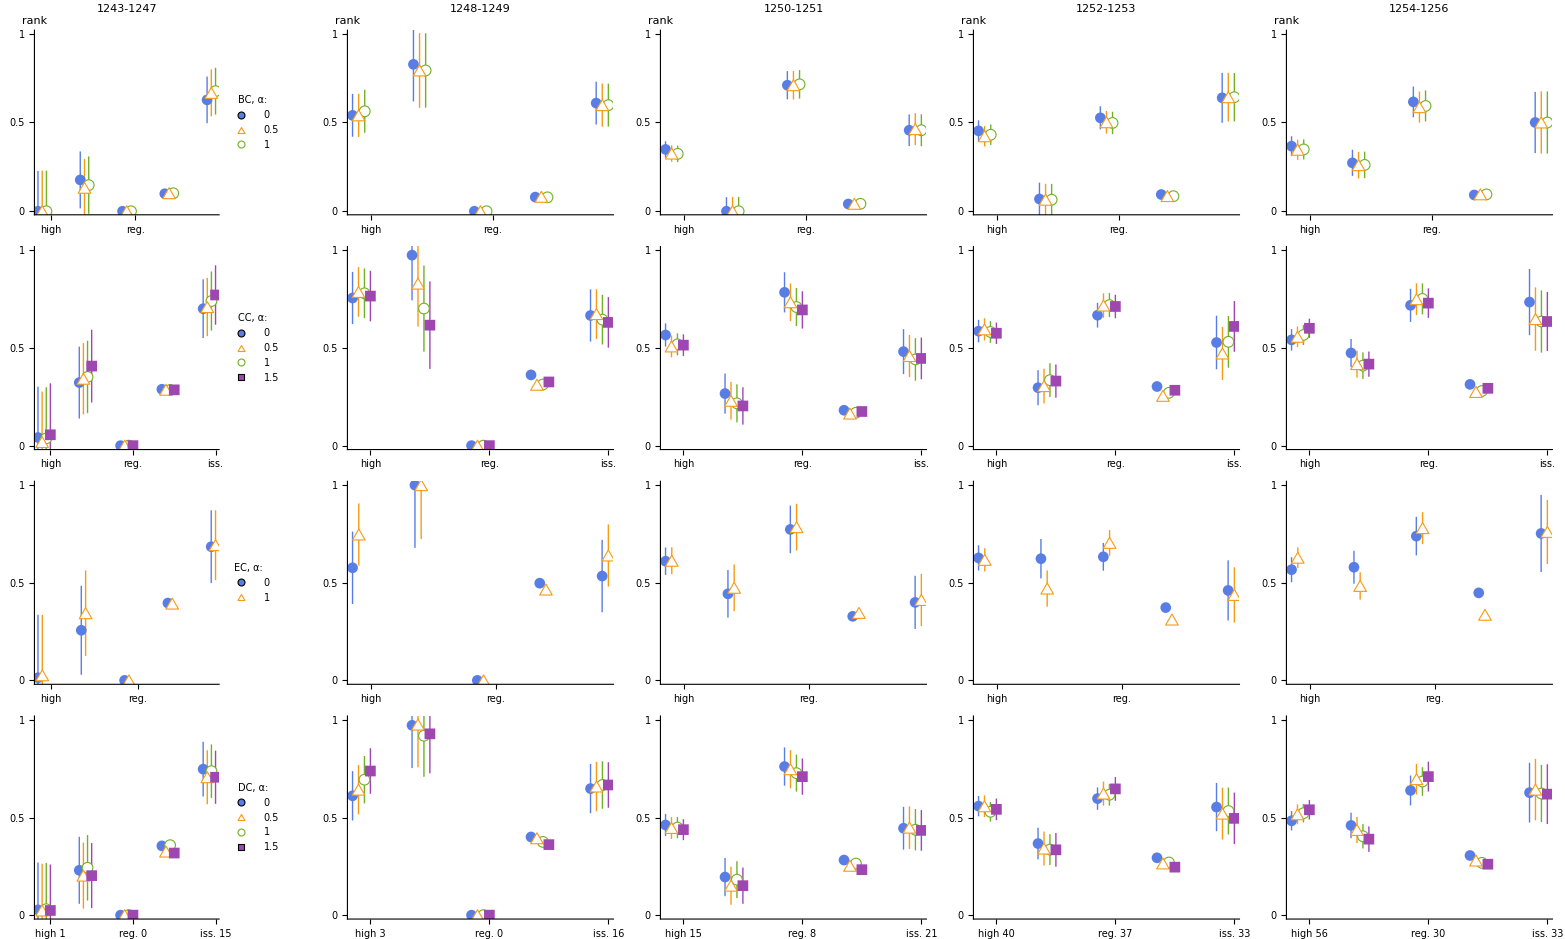

```mathematica
cent={{"b0","b0.5","b1"},{(*"c-1",*)"c0","c0.5","c1","c1.5"},{"e0","e1"},{"d0","d0.5","d1","d1.5"}};
Grid@Table[
Table[
funcNo={"high","low","regional","witness","vydavatel"}/.Normal@funcDS[c,1,Select[#witness+#high+#low+#regional+#vydavatel+#mention>0&],{"witness","high","low","regional","vydavatel"}][Total];
Show[
ListPlot[
Table[MapIndexed[{#2[[1]]+i/10,Around@@#1}&,res[c,centlist[[i]]][[{2,3,4,1,5}]]]
,{i,1,Length@centlist}],PlotStyle->ccolors[[{1,2,4,5}]],PlotMarkers->mmarkers[[{1,2,4,5}]],PlotLegends->If[c==1,Placed[PointLegend[(Style[""<>StringDrop[#,1],FontSize->14,FontFamily->"Helveticae",Black]&/@centlist),LegendLabel->Style[Switch[StringTake[centlist[[1]],1],"b","BC","d","DC","e","EC","c","CC"]<>", α:",FontSize->14,FontFamily->"Helveticae",Black,Bold]],{.6,.7}](*Placed[(Style[Switch[StringTake[#,1],"b","BC","d","DC","e","EC","c","CC"]<>", α="<>StringDrop[#,1],FontSize->14,FontFamily->"Helveticae",Black]&/@centlist),{.6,.8}]*),None],PlotLabel->If[centlist=={"b0","b0.5","b1"},ToString@segments[[c]]<>"-"<>ToString[segments[[c+1]]-1],None]
],PlotRange->{Full,{0,1}},AxesStyle->Directive[FontSize->16,FontFamily->"Helveticae",Black],AxesLabel->If[centlist=={"b0","b0.5","b1"},{None,"rank"},None],LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},
Ticks->If[centlist=={"d0","d0.5","d1","d1.5"},{{{1.4,"high\n"<>ToString[funcNo[[1]]],{0.02,0}},{2.4,"low\n"<>ToString[funcNo[[2]]],{0.02,0}},{3.4,"reg.\n"<>ToString[funcNo[[3]]],{0.02,0}},{4.4,"wit.\n"<>ToString[funcNo[[4]]],{0.02,0}},{5.4,"iss.\n"<>ToString[funcNo[[5]]],{0.02,0}}},{0,.5,1}},{{{1.4,"high",{0.02,0}},{2.4,"low",{0.02,0}},{3.4,"reg.",{0.02,0}},{4.4,"wit.",{0.02,0}},{5.4,"iss.",{0.02,0}}},{0,.5,1}}](*{{{1.4,Rotate["high",Pi/4],{0.02,0}},{2.4,Rotate["low",Pi/4],{0.02,0}},{3.4,Rotate["regional",Pi/4],{0.02,0}},{4.4,Rotate["witness",Pi/4],{0.02,0}},{5.4,Rotate["issuer",Pi/4],{0.02,0}}},{0,.5,1}}*),TicksStyle->Directive[FontSize->16,FontFamily->"Helveticae",Black],GridLines->None(*{{0},{0}}*),ImageSize->250,AspectRatio->1
],{c,1,5}]
,{centlist,cent}]
```

```mathematica
nom["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
witness | 0.300593 | 0.0175692 | 17.1091 | 2.96076×10^-40
high | 0.605905 | 0.0490351 | 12.3566 | 4.29875×10^-26
low | 0.423503 | 0.0644448 | 6.57157 | 4.71149×10^-10
regional | 0.733232 | 0.0755682 | 9.70291 | 2.56071×10^-18
vydavatel | 0.640244 | 0.151136 | 4.2362 | 0.0000354838

#### Not used: Ranks as numerical variables

```mathematica
Do[
temp=funcDS[c,1,Select[#witness+#high+#low+#regional+#vydavatel+#mention>0&],{"witness","high","low","regional","vydavatel"(*,"mention"*),cent}];
nom=LinearModelFit[{{"witness","high","low","regional","vydavatel"}/.#&/@Normal@temp,Normal@temp[All,cent]},{witness,high,low,regional,vydavatel}];
res[c,cent]=nom["ParameterConfidenceIntervalTableEntries"][[All,{1,2}]];
,{c,1,5},{cent,{"strength","b","c","e"}}];
```

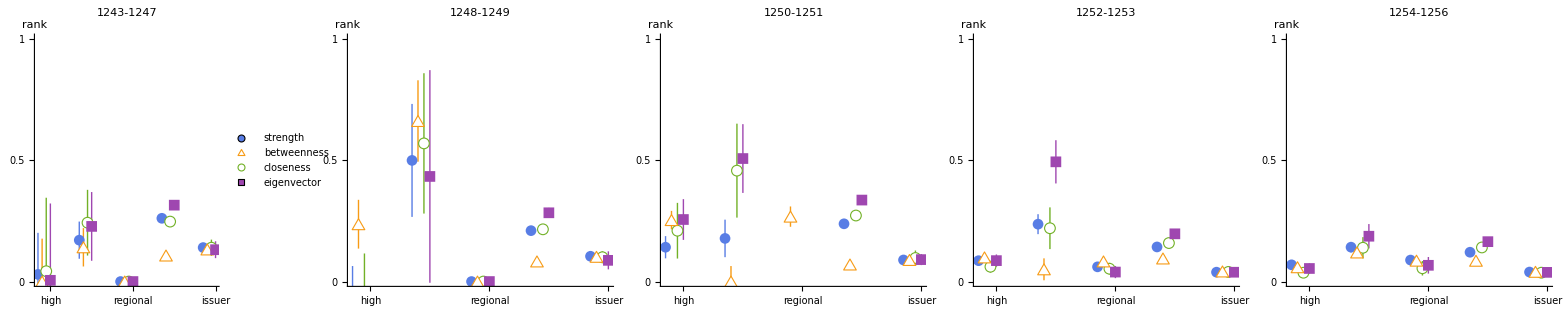

```mathematica
ccolors={Directive[RGBColor[0.34398, 0.49112, 0.89936],Thick],Directive[RGBColor[0.97, 0.606, 0.081],(*Dashing[0.015],*)Thick](*Directive[Black,Thick]*),Directive[RGBColor[0.09096, 0.6296, 0.85532],Thick(*,DotDashed*)],Directive[RGBColor[0.448, 0.69232, 0.1538](*,Dashing[0.03]*),Thick],Directive[RGBColor[0.62168, 0.2798, 0.6914],Thick(*,Dashing[0.015]*)],Directive[RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thickness[0.02]]};
marker2=Graphics[{RGBColor[0.34398, 0.49112, 0.89936],Disk[{1/2,1/2}]},ImageSize->11];
marker3=Graphics[{EdgeForm[Directive[Thick,RGBColor[0.97, 0.606, 0.081],Opacity[1]]],White,Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->13];
marker4=Graphics[{RGBColor[0.09096, 0.6296, 0.85532],Disk[{1/2,1/2}]},ImageSize->markSize];
marker5=Graphics[{EdgeForm[Directive[Thick,RGBColor[0.448, 0.69232, 0.1538],Opacity[1]]],White,Disk[{1/2,1/2}]},ImageSize->11];
marker1=Graphics[{RGBColor[0.62168, 0.2798, 0.6914],Polygon[-1/2+2{{0,0},{0,1},{1,1},{1,0}}]},ImageSize->11];
marker6=Graphics[{RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],Thick,Line[{{.5,-1},{.5,2}}]},ImageSize->0.5markSize];
mmarkers={marker2,marker3,marker4,marker5,marker1,marker6};
Grid@{Table[
Show[
ListPlot[
Table[MapIndexed[{#2[[1]]+i/10,Around@@#1}&,res[c,{"strength","b","c","e"}[[i]]][[{2,3,4,1,5}]]]
,{i,1,4}],PlotStyle->ccolors[[{1,2,4,5}]],PlotMarkers->mmarkers[[{1,2,4,5}]],PlotLegends->If[c==1,Placed[(Style[#,FontSize->14,FontFamily->"Helveticae",Black]&/@{"strength","betweenness","closeness","eigenvector"}),{.7,.8}],None],PlotLabel->ToString@segments[[c]]<>"-"<>ToString[segments[[c+1]]-1]
],PlotRange->{Full,{0,1}},AxesStyle->Directive[FontSize->16,FontFamily->"Helveticae",Black],AxesLabel->{None,"rank"},LabelStyle->{FontFamily->"Helveticae",FontSize->18,Black},
Ticks->{{{1.4,Rotate["high",Pi/4],{0.02,0}},{2.4,Rotate["low",Pi/4],{0.02,0}},{3.4,Rotate["regional",Pi/4],{0.02,0}},{4.4,Rotate["witness",Pi/4],{0.02,0}},{5.4,Rotate["issuer",Pi/4],{0.02,0}}},{0,.5,1}},TicksStyle->Directive[FontSize->16,FontFamily->"Helveticae",Black],GridLines->None(*{{0},{0}}*),ImageSize->250,AspectRatio->1
],{c,1,5}]}
```

#### Check particular cases

```mathematica
c=4;
funcDS[c,1,Select[#low>0&]]
Normal@funcDS[c,1,Select[#low>0&],"name"]
Tally/@makeFunc[segments[[c]],segments[[c+1]]-1][[Flatten[Position[names,#][[All,1]]&/@Flatten@Normal@funcDS[c,1,Select[#low>0&],"name"]]]]
```

Dataset[<>]

{Beneda,Budislav,Jan,Jindřich,Markvart, syn Wolframa,Sudomír z Žeravic,Wernhard z Našiměřic}

{{{0,32},{lovčí,2}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,33},{opavský sudí,1}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,32},{cúdař,2}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,34}},{{0,33},{1.,1}},{{0,34}},{{0,33},{znojemský sudí,1}},{{0,33},{arcidiákon znojemský,1}},{{0,32},{1.,1},{břeclavský komoří,1}},{{0,33},{brněnský sudí,1}}}